```mathematica
x=AbsoluteTime[]
(*CDF of the Gumbel distribution*)
```

3.666091372982209×10^9

```mathematica
Θt=Exp[-Exp[-t]]
```

ⅇ^(-ⅇ^-t)

```mathematica
(*CDF of LEVMIN model*)
```

```mathematica
Ft=Simplify[(Θt/.t-> ((t-μ)/θ))/(1-(Θt/.t-> (-μ/θ)))]
```

(ⅇ^(-ⅇ^((-t+μ)/θ)))/(1-ⅇ^(-ⅇ^(μ/θ)))

```mathematica
(*Mean value function*)
```

```mathematica
MVF=Simplify[ω Ft]
```

(ⅇ^(-ⅇ^((-t+μ)/θ)) ω)/(1-ⅇ^(-ⅇ^(μ/θ)))

```mathematica
(*Instantaneous failure rate or failure intensity*)
```

```mathematica
λt=D[MVF,t]
```

(ⅇ^(-ⅇ^((-t+μ)/θ)+(-t+μ)/θ) ω)/((1-ⅇ^(-ⅇ^(μ/θ))) θ)

```mathematica
(*Define vector of failure times for SYS1 dataset*)
```

```mathematica
(*242.46,248.76,502.44,526.56,564.18,1492.56,2026.74,2218.44,2230.2,2389.44,2408.58,3004.56,3480.78,3539.76,3545.58,3646.2,3652.5,3980.64,3985.2,3991.98,*)
(*tVec={4061.4,4640.52,5217.6,5849.52,5849.64,5997.84,6925.98,6969.84,6973.44,6973.74,7634.367,7802.247,7989.087,8268.131,8688.251,8756.051,9079.511,9191.531,9196.811,9831.072,9832.992,10735.332,10737.432,10741.632,10742.112,10919.172,10961.532,10998.552,11053.092,11388.612,11388.912,11540.952,11652.312,12144.072,12224.412,12542.472,12545.592,12550.992,12735.732,12751.152,12852.012,13087.148,13088.768,13710.428,14270.656,14775.076,14781.856,15027.676,15509.964,15939.624,16935.16,17010.28,17470.3,17502.46,17704.96,18022.78,18288.04,18324.22,18498.4,18518.14,18526.54,18566.8,18569.74,18578.44,18585.52,18649.54,18649.9,18734.74,18734.92,19643.26,19650.94,19709.8,19732.36,19740.64,20309.736,20379.396,20673.276,20680.176,20939.436,20943.216,21254.992,21366.028,21779.968,22051.588,22116.148,22415.548,22448.428,23406.388,24404.168,24404.228,24517.568,24984.548,25495.748,25771.748,25956.908,26280.848,26599.268,27377.228,27381.428,27954.568,27956.788,29194.588,29417.548,29525.848,29584.828,29604.928,29687.248,30049.408,30050.008,30059.008,31304.668,31321.468,32322.508,32322.656,32322.772,32323.012,32323.492,32324.332,32743.672,32743.792,32803.852,32890.732,32896.912,32897.092,32995.192,32998.492,33340.732,34452.052,34460.452,34552.132,35173.912,36049.612,36684.232,36684.652,37064.032,37082.032,37144.132,37152.952,37656.532,37932.352,38280.532,38285.632,38763.532,39399.952,39975.292,40197.652,40284.232,40286.992,40289.812,40291.372,40291.792,40292.992,40294.432,40401.472,40432.912,40737.172,40796.272,41064.232,41085.952,41154.712,41417.092,41421.652,41752.672,43474.972,43522.492,43823.662,43824.682,43992.682,44105.992,45719.542,45811.732,46258.072,46323.322,48223.942,48644.002,48889.282,50236.822};*)

(*3,33,146,227,342,351,353,444,556,571,709,759,836,*)
tVec = {860,968,1056,1726,1846,1872,1986,2311,2366,2608,2676,3098,3278,3288,4434,5034,5049,5085,5089,5089,5097,5324,5389,5565,5623,6080,6380,6477,6740,7192,7447,7644,7837,7843,7922,8738,10089,10237,10258,10491,10625,10982,11175,11411,11442,11811,12559,12559,12791,13121,13486,14708,15251,15261,15277,15806,16185,16229,16358,17168,17458,17758,18287,18568,18728,19556,20567,21012,21308,23063,24127,25910,26770,27753,28460,28493,29361,30085,32408,35338,36799,37642,37654,37915,39715,40580,42015,42045,42188,42296,42296,45406,46653,47596,48296,49171,49416,50145,52042,52489,52875,53321,53443,54433,55381,56463,56485,56560,57042,62551,62651,62661,63732,64103,64893,71043,74364,75409,76057,81542,82702,84566,88682};
```

```mathematica
(* Define failure count (n), time of last failure (tn) and sum of failure time vector sumT *)
```

```mathematica
n=Length[tVec];
tn=tVec[[n]];
sumT=∑_(i=1)^n tVec[[i]];
```

```mathematica
(*log-likelihood function*)
```

```mathematica
lnL=-(MVF/.{t->tn})+∑_(i=1)^n (Log[λt]/.{t->tVec[[i]]});
```

```mathematica
(*IECM*)
```

```mathematica
RLL=lnL/.ω-> n/(Ft/.t->tn);
```

```mathematica
θHat=D[RLL,θ];
μHat=D[RLL,μ];
```

```mathematica
ft=Simplify[D[Ft,t]]/.t->t[[i]];
```

Part::pkspec1: The expression i cannot be used as a part specification.

```mathematica
μInitial=Part[FindRoot[0==∑_(i=1)^n (D[Log[ft],μ])/.{θ->1,t->tVec},{μ,0}],1,2]
```

Part::partd: Part specification t⟦1⟧ is longer than depth of object.

Part::partd: Part specification t⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-19.0603

```mathematica
(*For Mathematica - Initial Estimate*)
∑_(i=1)^n (D[Log[ft],μ])
```

Part::partd: Part specification t⟦1⟧ is longer than depth of object.

Part::partd: Part specification t⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ⅇ^(ⅇ^(1/θ)-1/θ) (θ-1) (-ⅇ^1/1^2+1/(θ-1))+121+1
 |  |  |  |

```mathematica
θInitial=Part[FindRoot[0==∑_(i=1)^n (D[Log[ft],θ])/.{μ->μInitial,t->tVec},{θ,1}],1,2]
```

Part::partd: Part specification t⟦1⟧ is longer than depth of object.

Part::partd: Part specification t⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

21994.

```mathematica
(*For Mathematica - Initial Estimate*)
∑_(i=1)^n (D[Log[ft],θ])
```

Part::partd: Part specification t⟦1⟧ is longer than depth of object.

Part::partd: Part specification t⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1
 |  |  |  |

```mathematica
μInitial =8.52;
θInitial = 2048.512;
```

```mathematica
θrule={θInitial};
μrule={μInitial};
LLList=List[Re[RLL/.{θ->θrule[[1]],μ->μrule[[1]]}]];
bcList=List[{θrule[[Length[θrule]]],μrule[[Length[μrule]]]}];
LLerrorList=List[];
LLerror=1;
j=1;
Timing[While[LLerror> 10^-5,
AppendTo[θrule,Part[FindRoot[θHat==0/.μ->μrule[[Length[μrule]]],{θ,θrule[[j]]},MaxIterations->1000],1,2]];
AppendTo[bcList,{θrule[[Length[θrule]]],μrule[[Length[μrule]]]}];
AppendTo[μrule,Part[FindRoot[μHat==0/.θ->θrule[[Length[θrule]]],{μ,μrule[[j]]},MaxIterations->1000],1,2]];
AppendTo[bcList,{θrule[[Length[θrule]]],μrule[[Length[μrule]]]}];
AppendTo[LLList,Re[RLL/.{μ->μrule[[Length[μrule]]],θ->θrule[[Length[θrule]]]}]];
j=j+1;
AppendTo[LLerrorList,LLerror=Abs[LLList[[j]]-LLList[[j-1]]]];
];]
AbsoluteTime[]-x
```

{0.799726,Null}

5.140345

```mathematica
j
```

7

```mathematica
LLList[[j]]
```

-926.896

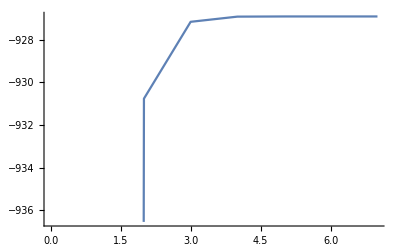

```mathematica
ListPlot[LLList,Joined->True]
```

```mathematica
θrule[[j]]
μrule[[j]]
```

18001.1

17426.4

```mathematica
ωmle=n/(Ft/.{t->tn,θ->θrule[[j]],μ->μrule[[j]]})
```

116.36

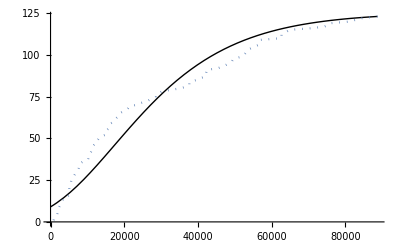

```mathematica
gFittedIECM=Plot[MVF/.{ω->ωmle,μ->μrule[[Length[μrule]]],θ->θrule[[Length[θrule]]]},{t,1,tVec[[n]]},PlotStyle->{Black,Thin,FontSize->30,Font->Helvetica}];gEmpirical=ListPlot[Transpose[{tVec,Table[i,{i,1,n}]}],PlotStyle->{Dotted,FontSize->30,Font->Helvetica},Joined->True];
Show[{gFittedIECM,gEmpirical}]
```

```mathematica
(*Faults remaining*)
```

```mathematica
ωmle-n
```

-6.63962

```mathematica
(*Reliability*)
```

```mathematica
R=Exp[-((MVF/.t->(tn+Δ))-MVF/.t->(tn))]/.{ω->ωmle,μ->μrule[[Length[μrule]]],θ->θrule[[Length[θrule]]]}
```

ⅇ^(123.-125.371 ⅇ^(-ⅇ^(0.0000555523 (-71255.6-Δ))))

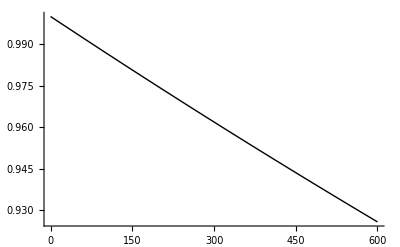

```mathematica
Plot[R,{Δ,0,600},PlotStyle->{Thin,Black}]
```

```mathematica
RLL/.{μ-> 24294.11,θ-> 21203.03}
```

-932.8

```mathematica
iteration={0,10,20,30,40,50,60,70,80,90,100};
LNLVal={0,(-1993.045-3183.991-1993.313-1983.92-1902.116)/5,(-3162.148-3544.428-2502.527-1690.885-1480.923)/5,(-1993.257-1993.245-3495.448-1826.67-1475.492)/5,
(-1993.355-1665.738-1993.357-1823.993-1822.073)/5,
(-1992.96-2460.933-1947.703-1993.072-1993.234)/5,
(-3353.775-3526.541-1936.748-3532.638-1993.019)/5,
(-1990.389-1993.019-1991.843-1968.389-1981.372)/5,
(-1981.374-3448.614-1947.66-1993.249-1904.889)/5,
(-1694.649-1993.204-1806.986-3163.742-1986.107)/5,
(-1992.828-1980.212-1992.695-1500.449-2502.556)/5};
ListPlot[LNLVal,iteration]
```

ListPlot::nonopt: Options expected (instead of {0,10,20,30,40,50,60,70,80,90,100}) beyond position 1 in ListPlot[{0,-2211.28,-2476.18,-2156.82,«3»,-1985.,-2255.16,-2128.94,-1993.75},«1»]. An option must be a rule or a list of rules.

ListPlot[{0,-2211.28,-2476.18,-2156.82,-1859.7,-2077.58,-2868.54,-1985.,-2255.16,-2128.94,-1993.75},{0,10,20,30,40,50,60,70,80,90,100}]

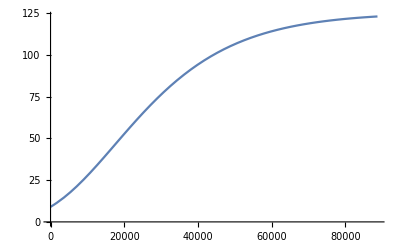

```mathematica
Plot[MVF/.{ω-> ωmle,μ-> μrule [[Length[μrule]]],θ-> θrule[[Length[θrule]]]},{t,0,tVec[[n]]}]
```